```mathematica
nguyen1[x_] := x^3 + x^2 + x;
nguyen2[x_] := x^4 + x^3 + x^2 + x;
nguyen3[x_] := x^5 +x^4 +x^3 + x^2 + x;
nguyen4[x_] := x^6 + x^5 +x^4 +x^3 + x^2 + x;
nguyen5[x_] := Sin[x^2] * Cos[x]-1;
nguyen6[x_] := Sin[x] + Sin[x+x^2];
nguyen7[x_] := Log[x+1] + Log[x^2+1];
nguyen8[x_] := Sqrt[x]
```

```mathematica
Print["Benchmark Equations"]
Do[Print[Simplify[eqn[x]]];,
 {eqn, {nguyen1, 
	nguyen2, 
	nguyen3,
	nguyen4,
	nguyen5,
	nguyen6,
	nguyen7,
	nguyen8
}}]
```

Benchmark Equations

x (1+x+x^2)

x (1+x+x^2+x^3)

x (1+x+x^2+x^3+x^4)

x (1+x+x^2+x^3+x^4+x^5)

-1+Cos[x] Sin[x^2]

Sin[x]+Sin[x (1+x)]

Log[1+x]+Log[1+x^2]

√x

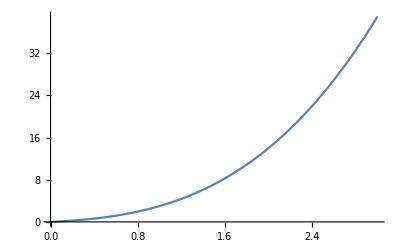

```mathematica
Plot[nguyen1[x], {x,0,3}]
```

```mathematica
rangeMin = -1.0;
rangeMax = 1.0;
numberSamples = 20;
numberTrials = 100;
Do[
evals  = {};
For[ii=1, ii<=numberTrials, ii++,
SeedRandom[ii];
myX = RandomReal[{rangeMin,rangeMax},{numberSamples}];
y = eqn[myX];

predFn = FindFormula[Transpose[{myX,y}],x,TargetFunctions->{Times, Log, Plus, Sin, Cos, Power}];

isCorrect =If[Simplify[Expand[eqn[x]] ==Expand[predFn]],1,0,0];
(*Print[Expand[eqn[x]]];
Print[Expand[predFn]];
Print[Expand[eqn[x]]-Expand[predFn]];*)
evals = Append[evals, isCorrect];

];
msg = StringJoin["Mean recovery = ", ToString[N[Mean[evals],4]]];
Print[Simplify[eqn[x]]];
Print[msg];,
{eqn, {nguyen1, 
	nguyen2, 
	nguyen3,
	nguyen4,
	nguyen5,
	nguyen6}
}]
rangeMin = 0.0;
rangeMax = 2.0;
numberSamples = 20;
Do[
evals  = {};
For[ii=1, ii<=numberTrials, ii++,
SeedRandom[ii];
myX = RandomReal[{rangeMin,rangeMax},{numberSamples}];
y = eqn[myX];

predFn = FindFormula[Transpose[{myX,y}],x,TargetFunctions->{Times, Log, Plus, Sin, Cos, Power}];

isCorrect =If[Simplify[Expand[eqn[x]] ==Expand[predFn]],1,0,0];
(*Print[Expand[eqn[x]]];
Print[Expand[predFn]];
Print[Expand[eqn[x]]-Expand[predFn]];*)
evals = Append[evals, isCorrect];

];
msg = StringJoin["Mean recovery = ", ToString[N[Mean[evals],4]]];
Print[Simplify[eqn[x]]];
Print[msg];,
{eqn, {nguyen7}
}]
rangeMin = 0.0;
rangeMax = 4.0;
numberSamples = 20;
Do[
evals  = {};
For[ii=1, ii<=numberTrials, ii++,
SeedRandom[ii];
myX = RandomReal[{rangeMin,rangeMax},{numberSamples}];
y = eqn[myX];

predFn = FindFormula[Transpose[{myX,y}],x,TargetFunctions->{Times, Log, Plus, Sin, Cos, Power}];

isCorrect =If[Simplify[Expand[eqn[x]] ==Expand[predFn]],1,0,0];
(*Print[Expand[eqn[x]]];
Print[Expand[predFn]];
Print[Expand[eqn[x]]-Expand[predFn]];*)
evals = Append[evals, isCorrect];

];
msg = StringJoin["Mean recovery = ", ToString[N[Mean[evals],4]]];
Print[Simplify[eqn[x]]];
Print[msg];,
{eqn, {nguyen8}
}]
```

x (1+x+x^2)

Mean recovery = 0.9700

x (1+x+x^2+x^3)

Mean recovery = 0.9900

x (1+x+x^2+x^3+x^4)

Mean recovery = 0.9900

x (1+x+x^2+x^3+x^4+x^5)

Mean recovery = 0.9800

-1+Cos[x] Sin[x^2]

Mean recovery = 0.0100

Sin[x]+Sin[x (1+x)]

Mean recovery = 0

Log[1+x]+Log[1+x^2]

Mean recovery = 0

√x

Mean recovery = 0.8700

```mathematica
numberTrials
```

numberTrials